```mathematica
omegac=100
```

100

```mathematica
beta=1.0
```

1.

```mathematica
Omega=1.0
```

1.

```mathematica
alpha=0.01
```

0.01

```mathematica
f[k_]=1/2*alpha*Exp[(-k/omegac)]*k*Coth[(beta*k/2)]/((k+Omega)*(k-Omega))
```

(0.005 ⅇ^(-k/100) k Coth[0.5 k])/((-1.+k) (1.+k))

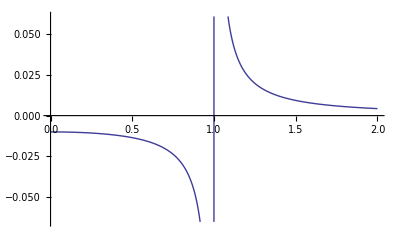

```mathematica
Plot[f[k],{k,0,2}]
```

```mathematica
NIntegrate[f[k],{k,0,Omega/2}]
```

-0.00551953

```mathematica
NIntegrate[f[k],{k,Omega/2,Omega-0.0001}] + NIntegrate[f[k],{k,Omega+0.0001,3*Omega/2}]
```

-0.00199281

```mathematica
NIntegrate[f[k], {k, 3*Omega/2, Infinity}]
```

0.0211823

```mathematica
NIntegrate[f[k],{k,0.999,0.9999}]+NIntegrate[f[k],{k,1.0001,1.001}]
```

-3.47958×10^-6

```mathematica
NIntegrate[f[k],{k,0,Omega/2}] + NIntegrate[f[k],{k,Omega/2,Omega-0.0001}] + NIntegrate[f[k],{k,Omega+0.0001,3*Omega/2}] + NIntegrate[f[k], {k, 3*Omega/2, Infinity}]
```

0.0136699